Auswertung für Praktikum: Luminescence Spectroscopy
In diesem Notebook findet die Auswertung der Daten statt. Zunächst werden eine hilfreiche Funktionen definiert um Redundanzen zu vermeiden und dann wird jeder Datensatz mit individuellen Parametern gefittet.

```mathematica
(* Lade ErrorBar Package *)
Needs["ErrorBarPlots`"];

(* Setze Directory wo Messdaten liegen*)
SetDirectory["/Users/chegerland/Desktop/Praktikum_LUM/Messung/"];

(* ----------------------------------------------------------------------- *)
(* ----------------------------- Funktionen ------------------------------ *)
(* ----------------------------------------------------------------------- *)

(* importdata: Schneide Datenpunkte mit Fehler = 0 raus (Probleme bei Fit) *)
importdata[data_]:=DeleteCases[
Select[#,UnequalTo[0]]&/@Transpose[{data[[All,2]],data[[All,3]],data[[All,4]]}],
x_/;Length[x]≠3];

(* Fitmodelle model(Gauß) und model2(Doppelgauß) *)
model[ampl_,x0_,sigm_,x_]:=ampl*1/Sqrt[2*Pi*sigm^2]*Exp[-(x-x0)^2/(2 sigm^2)];
model2[ampl_,x0_,sigm_,ampl2_,x02_,sigm2_,x_]:=ampl*1/Sqrt[2*Pi*sigm^2]*Exp[-(x-x0)^2/(2 sigm^2)]+ampl2*1/Sqrt[2*Pi*sigm2^2]*Exp[-(x-x02)^2/(2 sigm2^2)];

(* f: Erstelle Fits (Gauß und Doppelgauß) mit geschätzten Peakpositionen/Amplituden *)
f[data_,x0guess_,amplguess_,x02guess_]:={
NonlinearModelFit[Transpose[{data[[All,1]],data[[All,2]]}],model[ampl,x0,sigm,x],{sigm,{x0,x0guess},{ampl,amplguess}},x,Weights->1/data[[All,3]]^2],
NonlinearModelFit[Transpose[{data[[All,1]],data[[All,2]]}],model2[ampl,x0,sigm,ampl2,x02,sigm2,x],{sigm,{x0,x0guess},{ampl,amplguess},ampl2,{x02,x02guess},sigm2},x,Weights->1/data[[All,3]]^2]
};

(* g: Zeige Fits + Datenpunkte mit Fehlerbalken *)
g[data_,list_,index_]:=Show[
ErrorListPlot[data,PlotRange->Full],Plot[list[[index]][y],{y,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Orange,PlotRange->Full]
];

(* trim: Schneide vorne und hinten Daten ab für bessere Fits *)
trim[data_,front_,back_]:=DeleteCases[data,x_/; x[[1]]<front || x[[1]]>back];
```

```mathematica
(* ----------------------------------------------------------------------- *)
(* ----------------------------- Rechnungen ------------------------------ *)
(* ----------------------------------------------------------------------- *)

(* Importiere Daten in große Liste *)
data = {};
Importfiles = FileNames["*.dat"];
For[i=1,i≤Length[Importfiles],i++,AppendTo[data,importdata[Import[Importfiles[[i]]]]]];

(* initiiere Fitliste und hänge folgende Datensätze an *)
fits = {};
i=0;

(* Temperaturen *)
temperatures =Sort[{80,90,100,110,120,130,140,150,165,180,195,210,225,240,255}];

(* 100K *)
i=1;
data1=trim[data[[i]],0,635];
AppendTo[fits,f[data1,615,70000,610]];
g[data[[i]],fits[[i]],1]
g[data[[i]],fits[[i]],2]
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 110K *)
i=2;
data2=trim[data[[i]],0,635];
AppendTo[fits,f[data2,615,67000,628]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 120K *)
i=3;
data3=trim[data[[i]],0,635];
AppendTo[fits,f[data3,619,60000,628]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 130K *)
i=4;
data4=trim[data[[i]],0,637];
AppendTo[fits,f[data4,620,52000,630]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 140K *)
i=5;
data5=trim[data[[i]],0,640];
AppendTo[fits,f[data5,620,50000,632]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 150K *)
i=6;
data6=trim[data[[i]],0,640];
AppendTo[fits,f[data6,620,48000,629]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 165K *)
i=7;
data7=trim[data[[i]],0,642];
AppendTo[fits,f[data7,621,40000,632]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 180K *)
i=8;
data8=trim[data[[i]],0,642];
AppendTo[fits,f[data8,622,35000,615]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 195K *)
i=9;
data9=trim[data[[i]],605,645];
AppendTo[fits,f[data9,626,30000,619]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 210K *)
i=10;
data10=trim[data[[i]],607,645];
AppendTo[fits,f[data10,626,27000,619]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 225K *)
i=11;
data11=trim[data[[i]],610,650];
AppendTo[fits,f[data11,630,20000,620]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 240K *)
i=12;
data12=trim[data[[i]],610,650];
AppendTo[fits,f[data12,631,15000,622]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 255K *)
i=13;
data13=trim[data[[i]],615,652];
AppendTo[fits,f[data13,632,12000,622]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

 
(* 80K_10ms *)
i=14;
data14=trim[data[[i]],600,640];
AppendTo[fits,f[data14,618,80000,622]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 80K_1ms *)
i=15;
data15=trim[data[[i]],600,630];
AppendTo[fits,f[data15,618,80000,626]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 80K_50ms *)
i=16;
data16=trim[data[[i]],600,630];
AppendTo[fits,f[data16,618,80000,626]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];

(* 90K *)
i=17;
data17=trim[data[[i]],600,640];
AppendTo[fits,f[data17,618,75000,622]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
fits[[i,1]]["AdjustedRSquared"];
fits[[i,2]]["AdjustedRSquared"];
```

Part::partw: Part 1 of {} does not exist.

g[{}⟦1⟧,f[trim[{}⟦1⟧,0,635],615,70000,610],1]

Part::partw: Part 1 of {} does not exist.

g[{}⟦1⟧,f[trim[{}⟦1⟧,0,635],615,70000,610],2]

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

Part::partw: Part 4 of {} does not exist.

Part::partw: Part 5 of {} does not exist.

Part::partw: Part 6 of {} does not exist.

Part::partw: Part 7 of {} does not exist.

Part::partw: Part 8 of {} does not exist.

Part::partw: Part 9 of {} does not exist.

Part::partw: Part 10 of {} does not exist.

Part::partw: Part 11 of {} does not exist.

Part::partw: Part 12 of {} does not exist.

Part::partw: Part 13 of {} does not exist.

trim[{}⟦13⟧,615,652][ParameterTable]

632[ParameterTable]

Part::partw: Part 14 of {} does not exist.

Part::partw: Part 15 of {} does not exist.

Part::partw: Part 16 of {} does not exist.

Part::partw: Part 17 of {} does not exist.

```mathematica
(* Plot mit allen Fitkurven *)
allfitsplot = {};
For[i=1,i≤Length[fits],i++,AppendTo[allfitsplot,Plot[fits[[i]][[2]][y],{y,600,650},PlotRange->All,AxesLabel->{"λ [nm]","Intensität [a.u.]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14],ImageSize->Large]]]
allfitsplot=Delete[allfitsplot,{{15},{16}}];
allfitsplot = Show[allfitsplot];
Export["allfitsplot.eps",allfitsplot];
```

```mathematica
(* Plot mit Peaks-Temperatur *)
allpeaksplot={};
For[i=1,i≤Length[fits],i++,AppendTo[allpeaksplot,x0/.fits[[i,2]]["BestFitParameters"]]]
allpeaksplot=Delete[allpeaksplot,{{15},{16}}];
allpeaksplot=Sort[allpeaksplot];
allpeaks=ListPlot[Transpose[{temperatures,allpeaksplot}],PlotRange->All,AxesLabel->{"T [K]","λ [nm]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14],ImageSize->Large];
Export["peaktemp.eps",allpeaks];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[3.10052/(1-0.999999 ⅇ^(-0.00135141/T))]

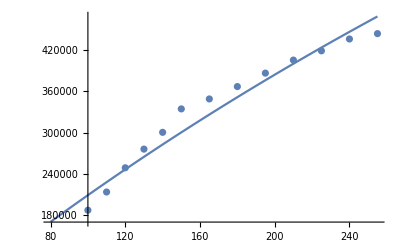

```mathematica
(* Plots mit maximalen Intensitäten - Temperatur *)
allmaxintplot={};
For[i=1,i≤Length[fits],i++,AppendTo[allmaxintplot,ampl/.fits[[i,2]]["BestFitParameters"]]]
allmaxintplot=Delete[allmaxintplot,{{15},{16}}];
allmaxintplot=Sort[allmaxintplot];
ListPlot[Transpose[{temperatures,allmaxintplot}]];

(* Plots mit integrierten Intensitäten - Temperatur *)
allintintplot = {};
For[i=1,i≤Length[fits],i++,AppendTo[allintintplot,Integrate[fits[[i,2]][x],{x,600,700}]]]
allintintplot=Delete[allintintplot,{{15},{16}}];
allintintplot=Sort[allintintplot];

intensityfit =NonlinearModelFit[Transpose[{temperatures,allintintplot}],I0/(1+a*Exp[-Ea1/( 8.617*10^-5*T)]),{I0,a,{Ea1,0.001}},T]


Show[Plot[intensityfit[T],{T,Min[temperatures],Max[temperatures]}],ListPlot[Transpose[{temperatures,allintintplot}]]]
```

```mathematica
intensityfit["BestFitParameters"]
```

{I0→3.10052,a→-0.999999,Ea1→1.16451×10^-7}

```mathematica
(* Plots mit Energie - Temperatur *)
allerrors = {};
For[i=1,i≤Length[fits],i++,AppendTo[allerrors,fits[[i,2]]["ParameterErrors"][[2]]]]
allerrors=Delete[allerrors,{{15},{16}}];
allerrors=Sort[allerrors]^2;
temporaer=Transpose[{Transpose[{temperatures,1240/allpeaksplot}],Map[ErrorBar,allerrors]}];
ErrorListPlot[{temporaer}];

(* Funktionen für geschätzte Zusammensetzung *)
Subscript[a, InP]=5.8687;
Subscript[a, GaP]=5.4505;
Subscript[a, GaAs]=5.65325;
Subscript[Eg, InP][T_]:=1.421 - 4.9*10^-4*T^2/(T+327);
Subscript[Eg, GaP][T_]:=2.34 - 6*10^-4*T^2/(T+460);
Clear[x];
x=First[x/.Solve[Subscript[a, GaAs]==x*Subscript[a, GaP]+(1-x)*Subscript[a, InP],x]];

(* Fit für Varshnigleichung + Test für Berechnung im Praktikum *)
nlm = NonlinearModelFit[Transpose[{temperatures,1240/allpeaksplot}],E0-α*T^2/(T+β),{E0,α,β},T,Weights->1/allerrors];
energtemp =Show[Plot[{nlm[T],x*Subscript[Eg, GaP][T]+(1-x)*Subscript[Eg, InP][T]},{T,Min[temperatures],Max[temperatures]},PlotRange->All,AxesLabel->{"T [K]","E_g [eV]"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14],ImageSize->Large,AxesOrigin->{Min[temperatures],1.83}],ErrorListPlot[{temporaer}]];
Export["energtemp.eps",energtemp];
```